Вершины многоугольника

{{31,13},{13,3},{22,18},{11,10},{5,31},{28,15},{15,26}}

Точка

{23,10}

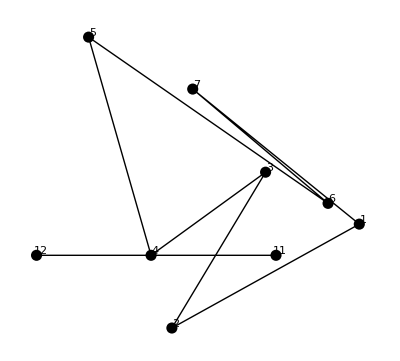

```mathematica
n=7;
a=1;
While[a≠0,{a=0;
P=Table[{RandomInteger[{3,35}],RandomInteger[{3,35}]},{n}];
For[i=1,i≤n-2,i++,For[j=i+2,j≤n,j++,{
If[j==n,{det1=Det[{P[[1]]-P[[j]],P[[i]]-P[[j]]}];
det2=Det[{P[[1]]-P[[j]],P[[i+1]]-P[[j]]}];
det3=Det[{P[[i+1]]-P[[i]],P[[j]]-P[[i]]}];
det4=Det[{P[[i+1]]-P[[i]],P[[1]]-P[[i]]}];
If[det1==0&&det2==0&&det3==0&&det4==0,If[(P[[j]][[1]]-P[[i]][[1]])*(P[[1]][[1]]-P[[i]][[1]])+(P[[j]][[2]]-P[[i]][[2]])*(P[[1]][[2]]-P[[i]][[2]])≤0||(P[[j]][[1]]-P[[i+1]][[1]])*(P[[1]][[1]]-P[[i+1]][[1]])+(P[[j]][[2]]-P[[i+1]][[2]])*(P[[1]][[2]]-P[[i+1]][[2]])≤0||(P[[i+1]][[1]]-P[[j]][[1]])*(P[[i]][[1]]-P[[j]][[1]])+(P[[i+1]][[2]]-P[[j]][[2]])*(P[[i]][[2]]-P[[j]][[2]])≤0||(P[[i+1]][[1]]-P[[1]][[1]])*(P[[i]][[1]]-P[[1]][[1]])+(P[[i+1]][[2]]-P[[1]][[2]])*(P[[i]][[2]]-P[[1]][[2]])≤0,a++,a=a],If[det1*det2<  0&&det3*det4≤  0,a++]]}]
If[j≠n,{det1=Det[{P[[j+1]]-P[[j]],P[[i]]-P[[j]]}];
det2=Det[{P[[j+1]]-P[[j]],P[[i+1]]-P[[j]]}];
det3=Det[{P[[i+1]]-P[[i]],P[[j]]-P[[i]]}];
det4=Det[{P[[i+1]]-P[[i]],P[[j+1]]-P[[i]]}];
If[det1==0&&det2==0&&det3==0&&det4==0,If[(P[[j]][[1]]-P[[i]][[1]])*(P[[j+1]][[1]]-P[[i]][[1]])+(P[[j]][[2]]-P[[i]][[2]])*(P[[j+1]][[2]]-P[[i]][[2]])≤0||(P[[j]][[1]]-P[[i+1]][[1]])*(P[[j+1]][[1]]-P[[i+1]][[1]])+(P[[j]][[2]]-P[[i+1]][[2]])*(P[[j+1]][[2]]-P[[i+1]][[2]])≤0||(P[[i+1]][[1]]-P[[j]][[1]])*(P[[i]][[1]]-P[[j]][[1]])+(P[[i+1]][[2]]-P[[j]][[2]])*(P[[i]][[2]]-P[[j]][[2]])≤0||(P[[i+1]][[1]]-P[[j+1]][[1]])*(P[[i]][[1]]-P[[j+1]][[1]])+(P[[i+1]][[2]]-P[[j+1]][[2]])*(P[[i]][[2]]-P[[j+1]][[2]])≤0,a++,a=a],If[det1*det2≤ 0&&det3*det4≤ 0,a++]]}]}]]}]
Print["Вершины многоугольника"];
P
Print["Точка"];
p0={RandomInteger[{10,45}],RandomInteger[{10,21}]}
p1={0,p0[[2]]};
p={p0,p1};
Graphics[{Line[Append[P,P[[1]]]],PointSize[0.02],Line[p],Point/@P,Point/@p,MapIndexed[Text[#2[[1]],#1+{.4,.4}]&,P],MapIndexed[Text[#2[[1]]+10,#1+{.4,.4}]&,p]}]
```

```mathematica
b=0; (*для проверки пересечений*)
d=0; (*для проверки совпадает ли точка с какой-либо вершиной*)
For[j=1,j≤n,j++,{
If[P[[j]]==p, d++]
}]
If [d==0, {
For[j=1,j≤n,j++,{
det = Det[{p1-p0, P[[j]]-p0}] ;
If[det==0, {
If[j==1,jm=n,jm=j-1];
If[j==n,jp=1,jp=j+1];
det11 = Det[{p1-p0, P[[jm]]-p0}] ;
det12 = Det[{p1-p0, P[[jp]]-p0}] ;
If[det12<0&&det11>0||det12>0&&det11<0,b++]
}]}]
For[j=1,j≤n,j++,{
If[j==n,{det1=Det[{P[[1]]-P[[j]],p0-P[[j]]}];
det2=Det[{P[[1]]-P[[j]],p1-P[[j]]}];
det3=Det[{p1-p0,P[[j]]-p0}];
det4=Det[{p1-p0,P[[1]]-p0}];
If[det1==0&&det2==0&&det3==0&&det4==0,If[(P[[j]][[1]]-p0[[1]])*(P[[1]][[1]]-p0[[1]])+(P[[j]][[2]]-p0[[2]])*(P[[1]][[2]]-p0[[2]])≤0||(P[[j]][[1]]-p1[[1]])*(P[[1]][[1]]-p1[[1]])+(P[[j]][[2]]-p1[[2]])*(P[[1]][[2]]-p1[[2]])≤0||(p1[[1]]-P[[j]][[1]])*(p0[[1]]-P[[j]][[1]])+(p1[[2]]-P[[j]][[2]])*(p0[[2]]-P[[j]][[2]])≤0||(p1[[1]]-P[[1]][[1]])*(p0[[1]]-P[[1]][[1]])+(p1[[2]]-P[[1]][[2]])*(p0[[2]]-P[[1]][[2]])≤0,b++,b=b],If[det1*det2<  0&&det3*det4<  0,b++]]}]
If[j≠n,{det1=Det[{P[[j+1]]-P[[j]],p0-P[[j]]}];
det2=Det[{P[[j+1]]-P[[j]],p1-P[[j]]}];
det3=Det[{p1-p0,P[[j]]-p0}];
det4=Det[{p1-p0,P[[j+1]]-p0}];
If[det1==0&&det2==0&&det3==0&&det4==0,If[(P[[j]][[1]]-p0[[1]])*(P[[j+1]][[1]]-p0[[1]])+(P[[j]][[2]]-p0[[2]])*(P[[j+1]][[2]]-p0[[2]])≤0||(P[[j]][[1]]-p1[[1]])*(P[[j+1]][[1]]-p1[[1]])+(P[[j]][[2]]-p1[[2]])*(P[[j+1]][[2]]-p1[[2]])≤0||(p1[[1]]-P[[j]][[1]])*(p0[[1]]-P[[j]][[1]])+(p1[[2]]-P[[j]][[2]])*(p0[[2]]-P[[j]][[2]])≤0||(p1[[1]]-P[[j+1]][[1]])*(p0[[1]]-P[[j+1]][[1]])+(p1[[2]]-P[[j+1]][[2]])*(p0[[2]]-P[[j+1]][[2]])≤0,b++,b=b],If[det1*det2< 0&&det3*det4< 0,b++]]}]}]

If[EvenQ[b],Print["Вне"],Print["В"]]},"Точка совпадает c вершиной многоугольника"];
```

В